# Introduction to Computational Physical Chemistry

© 2017 by Joshua Schrier and University Science Books  (Version: 25 July 2017)
Publisher’s Website: http://www.uscibooks.com/schrier.htm

## Appendix B - Data Analysis

## B.1 DATA REPRESENTATIONS

### B.1.1 Lists as data structures

```mathematica
PVdata={{16.56,1},{1.561,10},{0.7232,20},{0.4402,30},
{0.2929,40},{0.1978,50}};
```

```mathematica
TableForm[ PVdata,
TableHeadings->{None,{"Volume (L)","Pressure (atm)"}} ]
```

Volume (L) | Pressure (atm)
16.56 | 1
1.561 | 10
0.7232 | 20
0.4402 | 30
0.2929 | 40
0.1978 | 50

```mathematica
PVdata[[2]]
```

{1.561,10}

```mathematica
PVdata[[2,1]]
```

1.561

```mathematica
PVdata[[2,2]]
```

10

```mathematica
Length[PVdata]
```

6

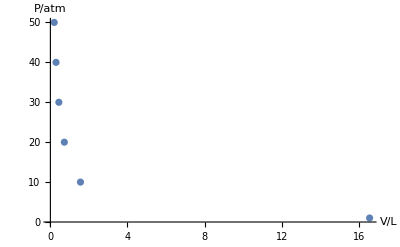

```mathematica
g1=ListPlot[ PVdata,
AxesLabel->{"V/L","P/atm"},PlotRange->All]
```

### B.1.2 Importing from files

“As an example, download a CSV file containing the temperature-dependent heat capacity of ammonia gas from http://hdl.handle.net/10066/17736 and save the AmmoniaHeatCapacity.csv file to the Downloads folder on your computer. Import[] the file into Mathematica by specifying the path to the file as the argument”

```mathematica
data=Import["~/Downloads/AmmoniaHeatCapacity.csv"]
```

{{T/K,Cp/J/K/mol},{300,35.56},{400,38.82},{500,41.68},{600,44.38},{700,47},{800,49.59},{900,52.15},{1000,54.7}}

“(This assumes that you are using a Mac or Linux computer. Paths are specified slightly differently in Windows. If you know how to specify paths, you can simply type the string, similar to what is shown in the example. Alternatively, the Insert>>File Path . . . menu opens a file browser that can be used to select the file, and returns the appropriate path as a string.)”

```mathematica
AmmoniaHeatCapacity=Drop[data,1]
```

{{300,35.56},{400,38.82},{500,41.68},{600,44.38},{700,47},{800,49.59},{900,52.15},{1000,54.7}}

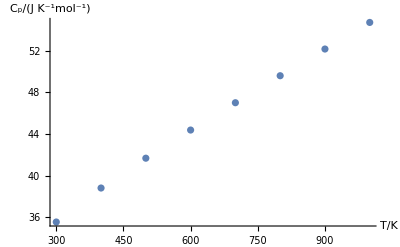

```mathematica
g2=ListPlot[ AmmoniaHeatCapacity,
AxesLabel->{"T/K","C_p/(J K^-1mol^-1)"}]
```

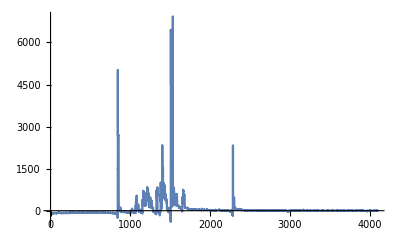

```mathematica
data=Import["http://www.jcamp-dx.org/lisms/cc/bruker1.dx"];
ListPlot[ data[[1]],
Joined->True,
PlotMarkers->None,PlotRange->All]
```

```mathematica
TableForm[
Import["http://www.jcamp-dx.org/lisms/cc/bruker1.dx",
"Metadata"][[1,1;;10]] ]
```

TITLE→1D WINNMR
JCAMPDX→5.
DATA TYPE→NMR SPECTRUM
DATA CLASS→XYDATA
ORIGIN→WINNMR 1D
OWNER→guest
.OBSERVE FREQUENCY→200.13
.OBSERVE NUCLEUS→??
.ACQUISITION MODE→SEQUENTIAL
.AVERAGES→16

## B.2 INTERPOLATION

```mathematica
p=Interpolation[PVdata]
```

InterpolatingFunction[{{0.1978, 16.56}}, <>]

```mathematica
p[0.2]
```

49.73

```mathematica
p[0.001]
```

InterpolatingFunction::dmval: Input value {0.001} lies outside the range of data in the interpolating function. Extrapolation will be used.

83.2744

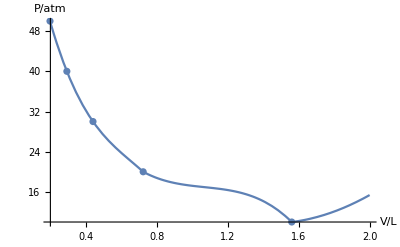

```mathematica
Show[
Plot[p[V],{V,0.2,2},
AxesLabel->{"V/L","P/atm"}],
g1 ]
```

```mathematica
Integrate[ p[V],{V,1,2}]
```

13.7578

```mathematica
D[ p[V],V]/.V->0.2
```

-122.303

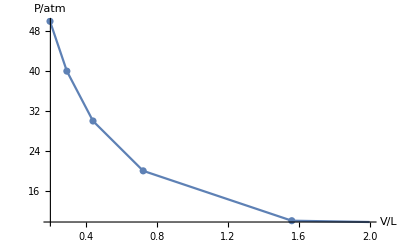

```mathematica
p2=Interpolation[PVdata,InterpolationOrder->1];
Show[ Plot[p2[V],{V,0.2,2},AxesLabel->{"V/L","P/atm"}],g1]
```

## B.3 REGRESSION ANALYSIS (“CURVE FITTING”)

### B.3.1 Linear regression

```mathematica
Fit[ AmmoniaHeatCapacity,{1,T,T^2,T^3},T]
```

23.956+0.0453154 T-0.0000249037 T^2+1.03535×10^-8 T^3

```mathematica
Cp[T_]:=23.956+0.0453154 T-0.0000249037 T^2+1.03535*10^-8 T^3
```

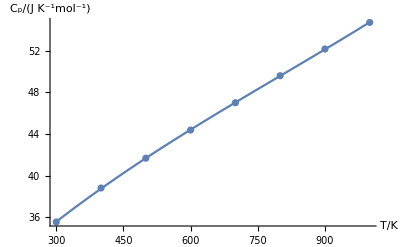

```mathematica
Show[ g2,Plot[Cp[T],{T,300,1000}] ]
```

### B.3.2 Nonlinear regression

```mathematica
T=207;(*temperature in kelvins*)
R=0.082057;(*gas constant in L.atm/K.mol*)
model=R*T/(V-b)-a/V^2;
fit1=FindFit[ PVdata,model,{a,b},V]
```

{a→-3.36792,b→1.19674}

```mathematica
fit2=FindFit[PVdata,model,{{a,0},{b,0}},V]
```

{a→2.7437,b→0.0564338}

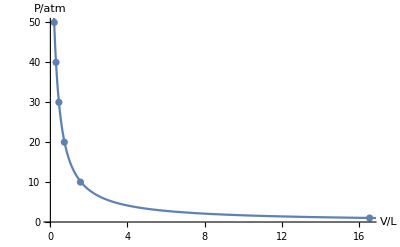

```mathematica
Show[ g1,Plot[model/.fit2,{V,0.19,17},PlotRange->All]]
```

## B.4 DESCRIPTIVE STATISTICS

```mathematica
data=ExampleData[{"Statistics","NickelContent"}]
```

{5.2,6.5,6.9,7,7,7,7.4,8,8,8,8,8.5,9,9,10,11,11,12,12,13.7,14,14,14,16,17,17,18,24,28,34,125}

```mathematica
Mean[data]
```

16.0065

```mathematica
Median[data]
```

11

```mathematica
StandardDeviation[data]
```

21.2691

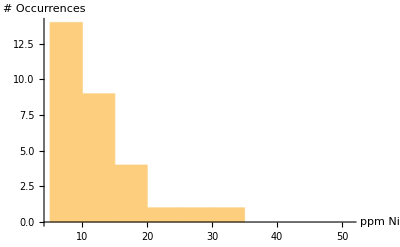

```mathematica
Histogram[ data,AxesLabel->{"ppm Ni","# Occurrences"}]
```